## Training

```mathematica
SetDirectory["/Volumes/MicroSD/Dropbox/PostDoc_SD/ZrC/Frenkel_classifier/Frenkels_classifier_training_structures/collective_PDFs"];
files={"pdf.70.4850.1_836.txt","pdf.129.4850.1_1141.txt","pdf.142.4850.1_891.txt","pdf.174.4850.1_851.txt","pdf.1126.4850.1_746.txt","pdf.PERF.4850.1_1071.txt"};
pdfData=Table[ReadList[files[[i]],{Number,Number,Number,Number,Number}],{i,1,6}];
names={"70","129","142","174","1126","PERF"};
fullNames={"Bound-dimer","Unbound-dimer","Unbound-trimer","Unbound-trimer","Unbound-tetramer","Perfect"};
header={"Methods","Bound-dimer","Bound-trimer","Unbound-dimer","Unbound-Trimer","Unbound-Tetramer","Perfect"};
volumes={"V=V(0.75T_C)","V=V(0.9T_C)"};
zrzr=Table[Transpose@{Transpose[pdfData[[i]]][[1]],Transpose[pdfData[[i]]][[2]]},{i,1,6}];
czr=Table[Transpose@{Transpose[pdfData[[i]]][[1]],Transpose[pdfData[[i]]][[3]]},{i,1,6}];
cc=Table[Transpose@{Transpose[pdfData[[i]]][[1]],Transpose[pdfData[[i]]][[4]]},{i,1,6}];
tot=Table[Transpose@{Transpose[pdfData[[i]]][[1]],Transpose[pdfData[[i]]][[5]]},{i,1,6}];
```

## Testing

```mathematica
SetDirectory["/Volumes/MicroSD/Dropbox/PostDoc_SD/ZrC/Frenkel_classifier/Frenkels_classifier_training_structures/test-data"];
filesTest={"1-Frenkel_500_222kp-6hr-9.602/pdf.70.4801.1_866.txt","2-Frenkel_500_222kp-6hr-9.700/pdf.test.4850.1_1021.txt"};
pdfDataTest=Table[ReadList[filesTest[[i]],{Number,Number,Number,Number,Number}],{i,1,2}];
```

```mathematica
zrzrTest=Table[Transpose@{Transpose[pdfDataTest[[i]]][[1]],Transpose[pdfDataTest[[i]]][[2]]},{i,1,2}];
czrTest=Table[Transpose@{Transpose[pdfDataTest[[i]]][[1]],Transpose[pdfDataTest[[i]]][[3]]},{i,1,2}];
ccTest=Table[Transpose@{Transpose[pdfDataTest[[i]]][[1]],Transpose[pdfDataTest[[i]]][[4]]},{i,1,2}];
totTest=Table[Transpose@{Transpose[pdfDataTest[[i]]][[1]],Transpose[pdfDataTest[[i]]][[5]]},{i,1,2}];
```

#### Visualise data

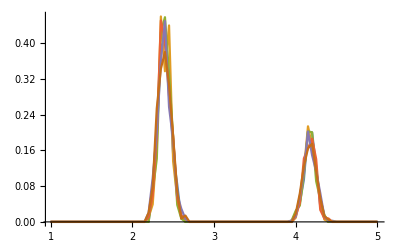

```mathematica
ListLinePlot[Partition[czr[[-1]],81][[5;;10]],PlotRange->All]
```

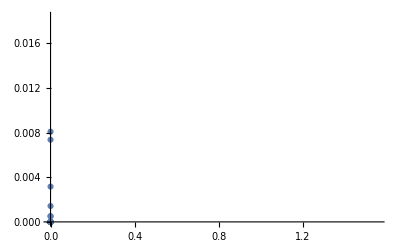

```mathematica
ListPlot[Transpose@{Transpose[Partition[czr[[-1]],81][[1]]][[2]],Sum[Transpose[Partition[czr[[-1]],81][[i]]][[2]],{i,1,5}]/5}]
```

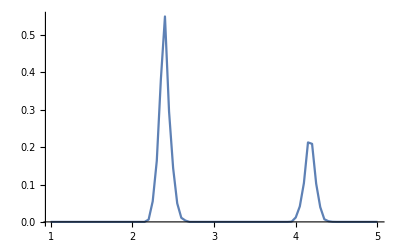

```mathematica
ListLinePlot[With[{n=10},Transpose@{Transpose[Partition[czr[[-1]],81][[1]]][[1]],Sum[Transpose[Partition[czr[[-1]],81][[i]]][[2]],{i,1,n}]/n}],PlotRange->All]
```

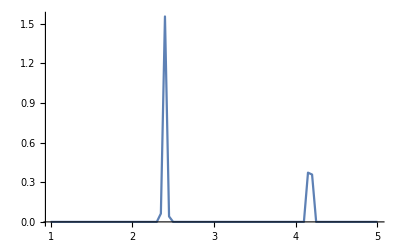
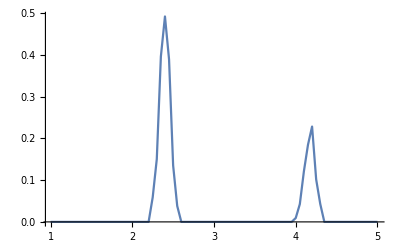
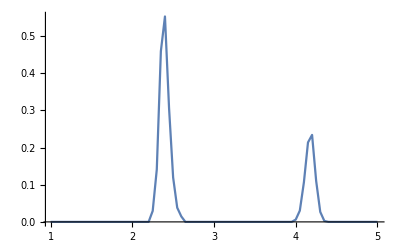
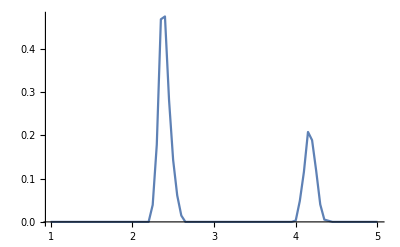
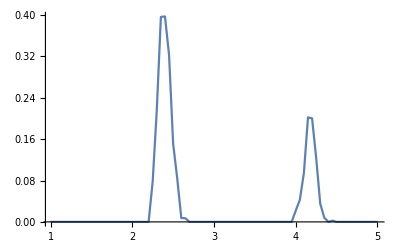
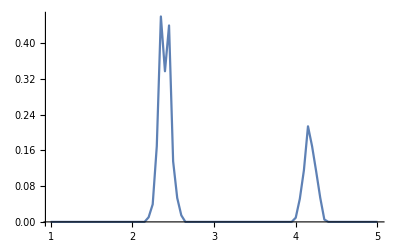
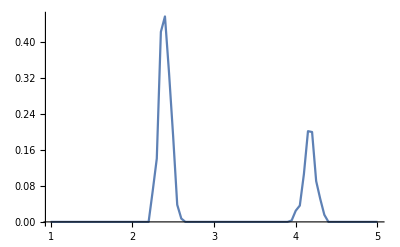
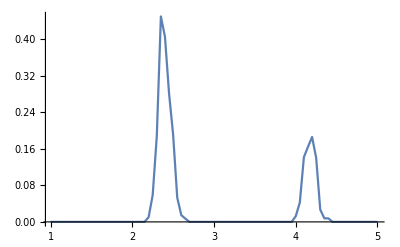

```mathematica
Table[ListLinePlot[Transpose@{Transpose[Partition[czr[[-1]],81][[1]]][[1]],Transpose[Partition[czr[[-1]],81][[j]]][[2]]},PlotRange->All],{j,1,15}]
```

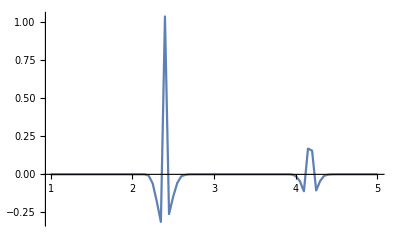
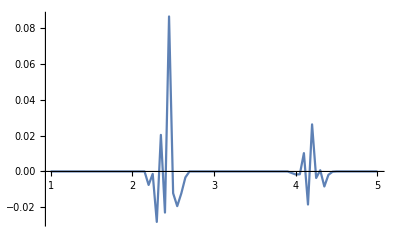
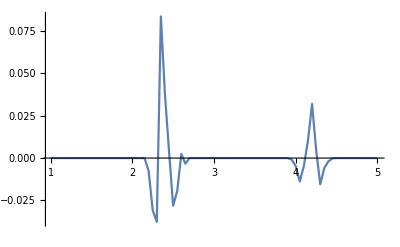
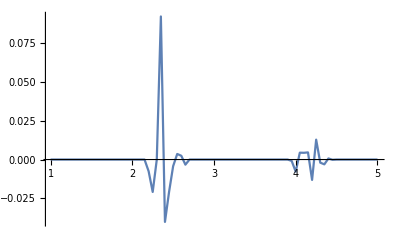
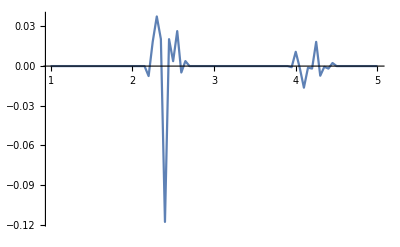
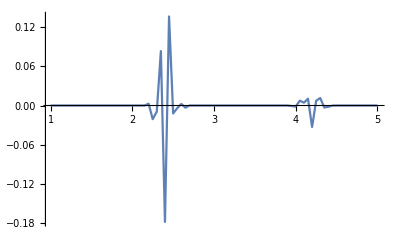
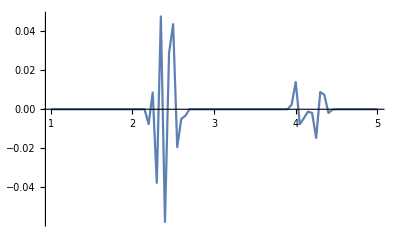
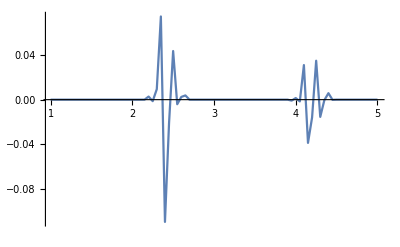

```mathematica
Table[ListLinePlot[Transpose@{Transpose[Partition[czr[[-1]],81][[1]]][[1]],Transpose[Partition[czr[[-1]],81][[j]]][[2]]-Sum[Transpose[Partition[czr[[-1]],81][[i]]][[2]],{i,1,15}]/15},PlotRange->All],{j,1,15}]
```

```mathematica
scores=With[{maxTypes=5},Table[results=With[{trainSize=99,valSize=50,method=methods[[i]]},trainSet=Join@@Table[Table[(Standardize[Transpose[Partition[cc[[type]],81][[timeStep]]][[2]]]-Standardize[Sum[Transpose[Partition[cc[[type]],81][[av]]][[2]],{av,2,101}]/100])->ToString@fullNames[[type]],{timeStep,1,trainSize}],{type,1,maxTypes}];

trainSet2=With[{trainSizeTest=15,maxTypesTest=2},Join@@Table[Table[Standardize[Transpose[Partition[ccTest[[typeTest]],81][[timeStepTest]]][[2]]]-Standardize[Sum[Transpose[Partition[ccTest[[typeTest]],81][[av]]][[2]],{av,2,101}]/100]->fullNames[[1]],{typeTest,1,maxTypesTest}],{timeStepTest,1,trainSizeTest}]];

c=Classify[Join[trainSet,trainSet2],Method->method,PerformanceGoal->"Speed"];
Table[Table[c[Standardize[Transpose[Partition[cc[[type]],81][[timeStep]]][[2]]]-Standardize[Sum[Transpose[Partition[cc[[type]],81][[av]]][[2]],{av,2,101}]/100]],{type,1,maxTypes}],{timeStep,trainSize,trainSize+valSize}]];
(*results for 10 training eras*)
accuracy=Table[{fullNames[[type]],Count[Transpose[results][[type]],Transpose[results][[type]][[1]]]/Length[Transpose[results][[type]]]//N},{type,1,maxTypes}];
Transpose[accuracy][[2]],{i,1,1}]];

finalResults=With[{maxTypes=5},Join[{header[[1;;maxTypes+1]]},Table[Flatten@Join[{methods[[i]],scores[[i]]}],{i,1,1}]]];
(*trainingSet=50,ValidationSet=100*)
finalResults//TableForm
```

Methods | Bound-dimer | Bound-trimer | Unbound-dimer | Unbound-Trimer | Unbound-Tetramer
LogisticRegression | 1. | 0.960784 | 0.980392 | 0.960784 | 1.

```mathematica
testOut=With[{trainSize=1,valSize=5,maxTypes=2},Table[Table[c[Standardize[Transpose[Partition[ccTest[[type]],81][[timeStep]]][[2]]]-Standardize[Sum[Transpose[Partition[cc[[type]],81][[av]]][[2]],{av,2,101}]/100]],{type,1,maxTypes}],{timeStep,trainSize,trainSize+valSize}]];
testOut//TableForm
```

Bound-dimer | Unbound-trimer
Unbound-trimer | Unbound-trimer
Unbound-trimer | Unbound-trimer
Unbound-trimer | Unbound-trimer
Unbound-trimer | Unbound-trimer
Unbound-trimer | Unbound-trimer